```mathematica
(* Discrete arrival of future funders *)
p = Exp[-δ*t];
mDot = r*m-x;
H = p*x^(1-η)/(1-η)+v*mDot
```

v (m r-x)+(ⅇ^(-t δ) x^(1-η))/(1-η)

```mathematica
(* Compute differentials *)
dx = D[H,x]
dm = D[H,m]
```

-v+ⅇ^(-t δ) x^-η

r v

```mathematica
(* Compute optimal variables *)
xStar = SolveValues[dx == 0, x][[1]]
vDot = -dm/.v->v[t];
vStar = DSolveValue[v'[t]== vDot, v[t],t];
xStar = xStar/.(v->vStar)/.C[1]-> c
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(t δ) v)^(-1/η)

(c ⅇ^(-r t+t δ))^(-1/η)

```mathematica
(* Solve transversality condition *)
xInt = Integrate[(xStar/.(t->τ))*Exp[-r*τ],{τ,0,t}]
```

((c^(-1/η)-ⅇ^(-r t) (c ⅇ^(t (-r+δ)))^(-1/η)) η)/(δ+r (-1+η))

```mathematica
((c^(-1/η)-ⅇ^(-r t) (c ⅇ^(t (-r+δ)))^(-1/η)) η)/(δ+r (-1+η))
```

((c^(-1/η)-ⅇ^(-r t) (c ⅇ^(t (-r+δ)))^(-1/η)) η)/(δ+r (-1+η))

```mathematica
(* Solve transversality condition *)
$Assumptions =  c>0&&η≠0&&η (-r+δ+r η)>0;
xLim = Limit[xInt, t->Infinity];
ϕ = q*B/(1-Exp[-n*r]);
transverse = B - xLim + ϕ
```

B+(B q)/(1-ⅇ^(-n r))-(c^(-1/η) η)/(δ+r (-1+η))

```mathematica
(*$Assumptions =  c>0&&η≠0&&η (-r+δ+r η)>0&& n >0 && r>0
cTransverse = Solve[transverse==0, c]*)
```

```mathematica
(* Define constant from transversality condition *)
cTransverse =(B(1 + q/(1-Exp[-n*r]))* (δ-r*(1-η))/η)^(-η)

(* Compute xStar and mDot *)
xStar = xStar/.(c->cTransverse)
mDot = mDot/.x->xStar;
```

((B (1+q/(1-ⅇ^(-n r))) (δ-r (1-η)))/η)^-η

(ⅇ^(-r t+t δ) ((B (1+q/(1-ⅇ^(-n r))) (δ-r (1-η)))/η)^-η)^(-1/η)

```mathematica
(* Solve diff equation and plot money available *)
mStar10 = DSolveValue[{m'[t]== (mDot/.m->m[t]), m[0]==B}, m[t],t];//FullSimplify
mStar20 = DSolveValue[{m'[t]== (mDot/.m->m[t]), m[10]==(mStar10/.t->10)+ q*B},m[t], t]//FullSimplify;
```

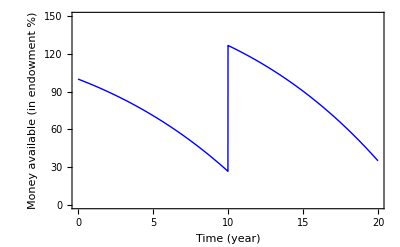

```mathematica
parameters ={η->2, δ->0.004,r->0.05,q -> 1,n->10,B ->100};
Plot[Piecewise[{{(mStar10/.parameters), 0<=t<10},{(mStar20/.parameters),10<=t<20}}], {t,0,20},PlotRange->{{0,20},{0,150}},Frame->True, FrameLabel->{"Time (year)", "Money available (in endowment %)"}, PlotStyle->{Blue,Thick}, LabelStyle->{FontSize->18}]
```

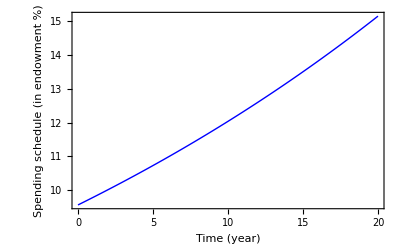

```mathematica
(* Plot Optimal spending schedule *)
Plot[xStar/.parameters, {t,0,20}, Frame->True, FrameLabel->{"Time (year)", "Spending schedule (in endowment %)"}, PlotStyle->{Blue,Thick}, LabelStyle->{FontSize->18}]
```

```mathematica
xStar10 = xStar/mStar10;
xStar20 = xStar/mStar20;
xS = Piecewise[{{xStar10,0<=t<=10},{ xStar20 ,10<=t<=20}}];
```

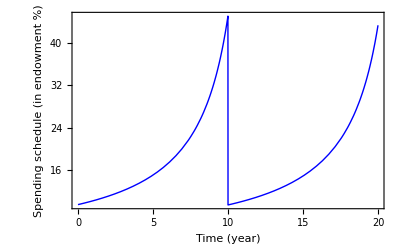

```mathematica
Plot[xS*100/.parameters, {t,0,20}, Frame->True, FrameLabel->{"Time (year)", "Spending schedule (in endowment %)"}, PlotStyle->{Blue,Thick}, LabelStyle->{FontSize->18}]
```

```mathematica
spent = NIntegrate[xStar/.parameters, {t,0,20} ]
```

242.823